# Analysis of the first piece of data from the dataglove

```mathematica
SetOptions[ListLinePlot, Frame->True, GridLines->Automatic, ImageSize->800, Axes->None];
data = Drop[Import["output.dat", "Table"], -1];
ScaleDown[point_] := N[point/1];
PlotData[point_] := Graphics3D[Arrow[{{0,0,0},ScaleDown[point]}], PlotRange->{{-1,1}, {-1,1},{-1,1}}]
dataNorm = N[ScaleDown /@ data];
dataMA = Transpose[{MovingAverage[dataNorm[[All, 1]], 10], MovingAverage[dataNorm[[All, 2]],10], MovingAverage[dataNorm[[All, 3]], 10]}];
```

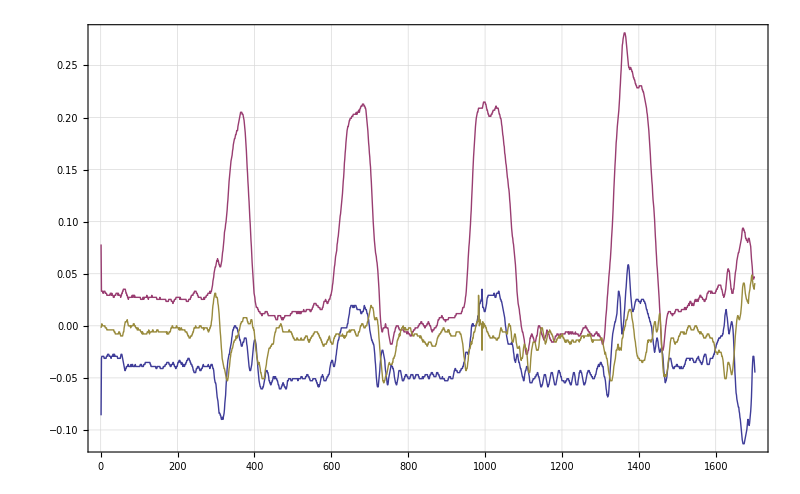

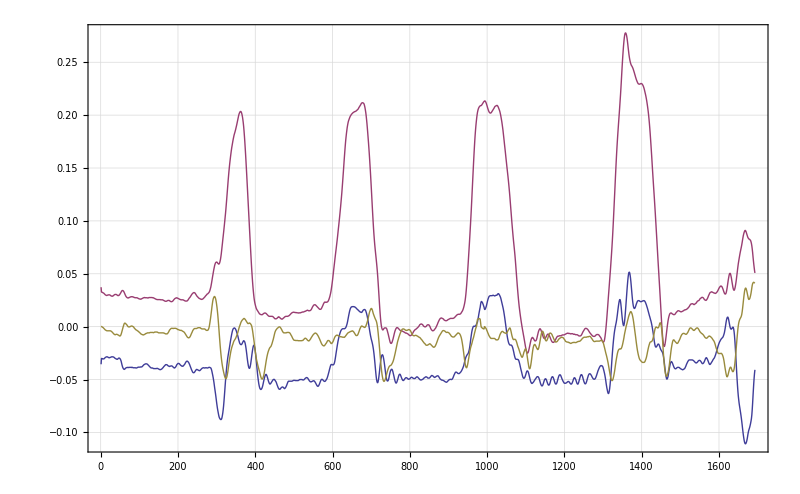

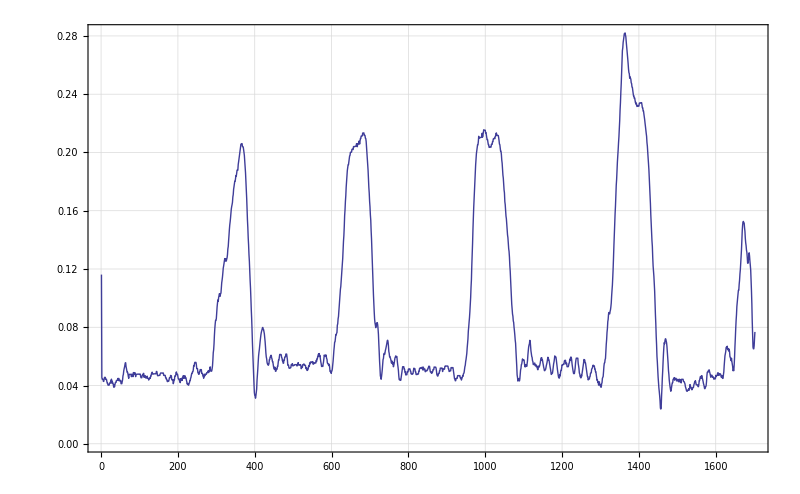

```mathematica
ListLinePlot[{dataNorm[[All, 1]], dataNorm[[All, 2]], dataNorm[[All, 3]]}, PlotRange->Full]
ListLinePlot[{dataMA[[All, 1]], dataMA[[All, 2]], dataMA[[All, 3]]}, PlotRange->Full]
ListLinePlot[Norm /@ dataNorm[[All, {1,2,3}]]]
```

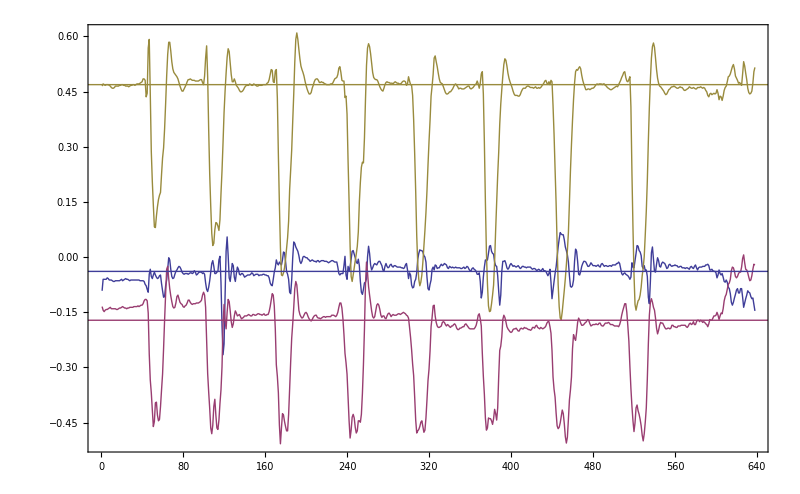

```mathematica
Model[x_,a_] := a;
zeroX = a/. FindFit[data[[All, 1]], Model[x,a], a,x];
zeroX = -20;
zeroY = a/. FindFit[data[[All, 2]], Model[x,a], a, x];
zeroY = -88;
zeroZ = a/. FindFit[data[[All, 3]], Model[x,a], a, x];
zeroZ = 240;

Show[ {
ListLinePlot[{dataNorm[[All, 1]], dataNorm[[All, 2]], dataNorm[[All, 3]]}],
Plot[Evaluate[ScaleDown[{zeroX, zeroY, zeroZ}]], {x,-100,700}]
}, GridLines->None]
```

```mathematica
dataNewNorm = Transpose[ScaleDown /@ {data[[All, 1]] - zeroX, data[[All, 2]] - zeroY, data[[All, 3]] - zeroZ}];
ListLinePlot[{dataNewNorm[[All, 1]], dataNewNorm[[All, 2]], dataNewNorm[[All, 3]]}, PlotRange->{{0,200}, Full}];

Manipulate[Block[{viewData = dataNewNorm[[158;;158+50, 3]]},
ListLinePlot[viewData, PlotRange->{-1,1}]
], {t,1,550,1}]
```

Part::take: Cannot take positions 158 through 208 in dataNewNorm.

ListLinePlot::lpn: dataNewNorm ⟦ 158 ;; 208, 3 ⟧ is not a list of numbers or pairs of numbers.

```mathematica
dataPossible = Select[Partition[dataNewNorm, 50, 1], Abs[#[[10,3]] ] > 0.02 &];
```

```mathematica
Model[x_,μ_, σ1_,σ2_,a_] := -a Exp[-(x-μ)^2/σ1]*Cos[(x-μ)/σ2];
godOnes = Function[i, Block[{dataTest = dataPossible[[i, All, 3]]}, 
Quiet[sol = FindFit[dataTest,Model[x,20,σ1,σ2, a],{a,σ1, σ2}, x]];
(*Show[{ListLinePlot[dataTest], Plot[Model[x,20,σ1,σ2, a]/.sol,{x,0,50}, PlotRange->Full]}]*)
If[(a/.sol) > 0.3, i, Missing[]]
]]/@Table[i,{i,1,Length[dataPossible]}];
godOnes = DeleteCases[godOnes, Missing[]];
```

```mathematica
godOnes
```

{1,2,3,4,5,32,33,34,35,36,37,58,59,60,61,62,63,64,65,94,95,96,97,98,99,100,101,102,125,126,127,128,129,130,155,156,157,158,159,160,161,188,189,190,191,192,193,194,216,217,218,219,220,221,222,223,224,225}

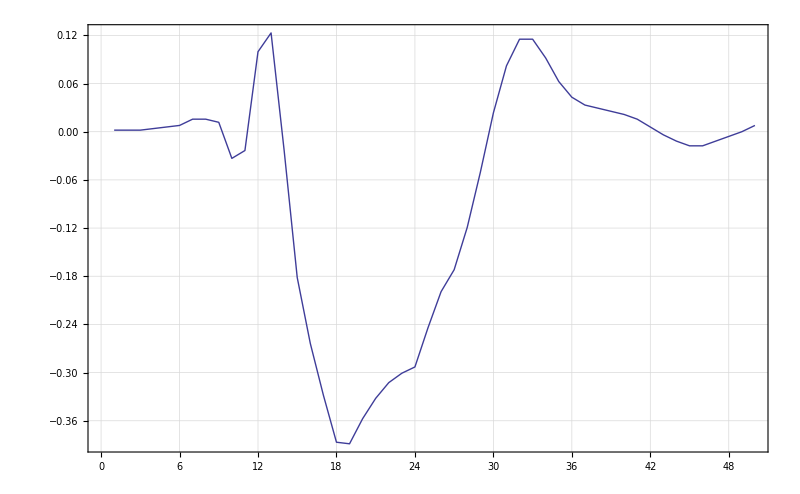
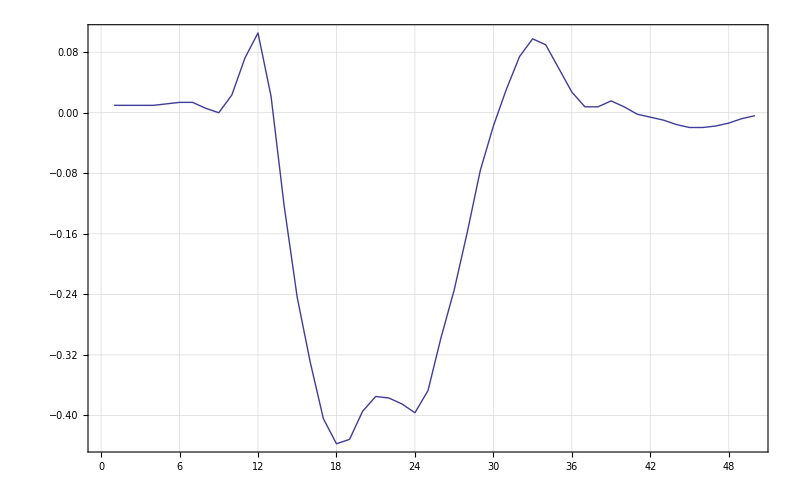
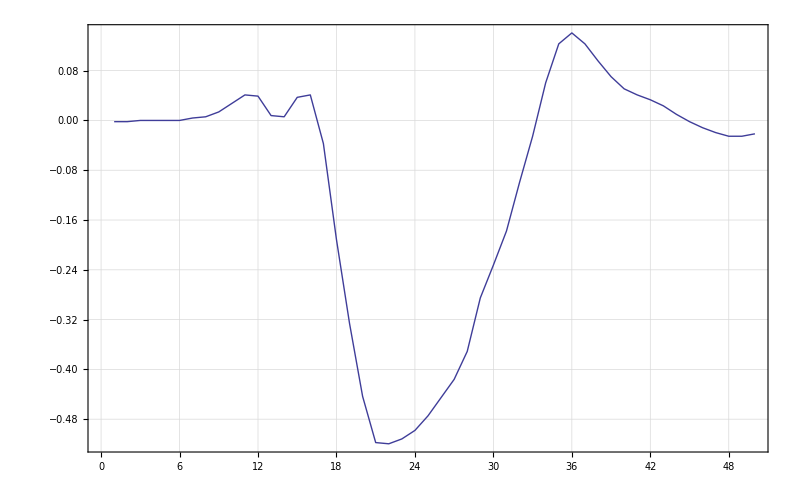
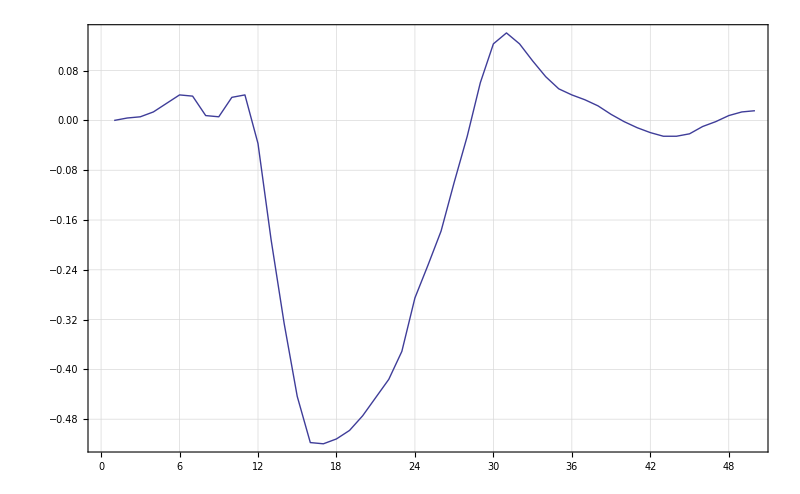
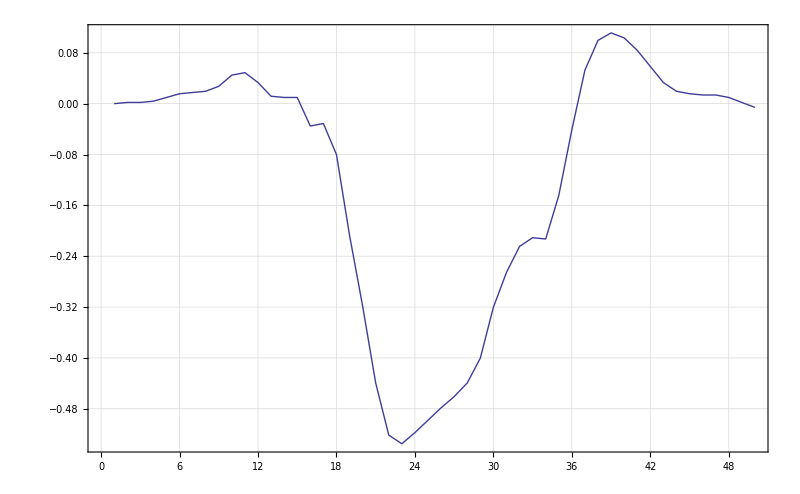
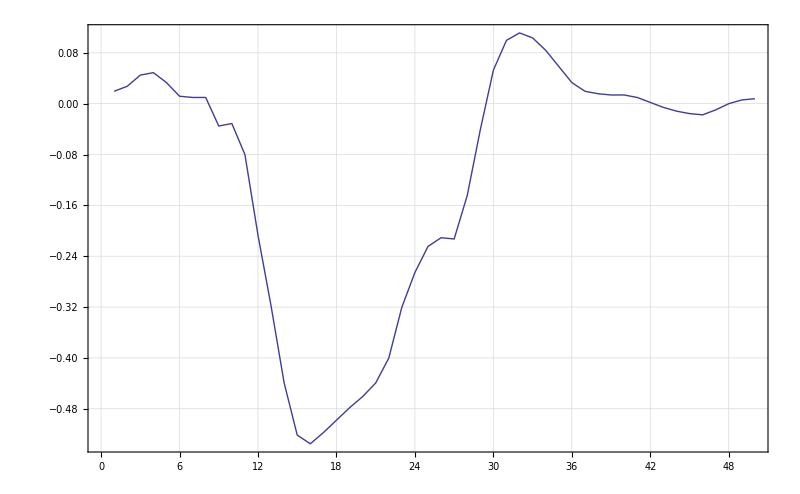
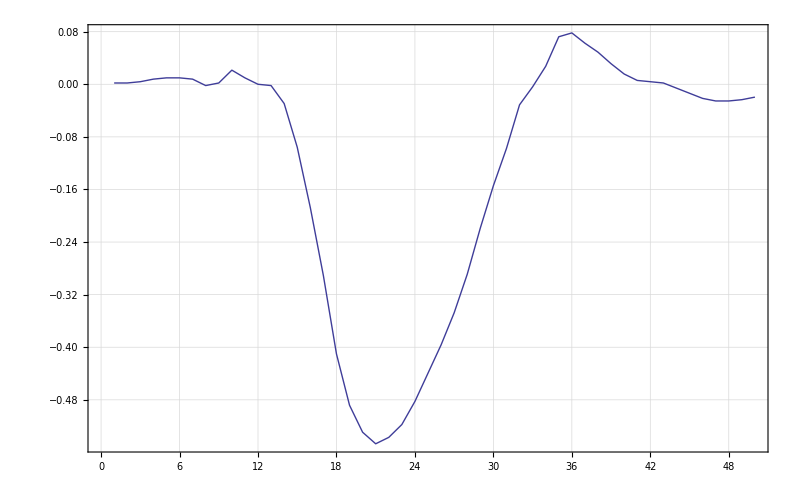
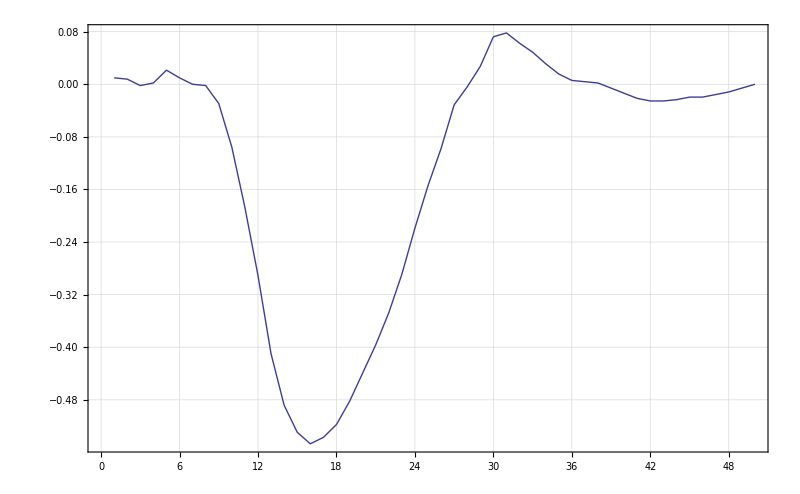

```mathematica
ListLinePlot[dataPossible[[#,All,3]]]&/@(#[[1]]&/@FindClusters[godOnes,15])
```